```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

```mathematica
ReV[r_,mD_,α_,σ_,c_]:=c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞},MaxRecursion->20]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

### Self energies

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],30];
```

```mathematica
Πpar[θ_,mD_,u_]:=SetPrecision[mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]),30];
```

```mathematica
Πper[θ_,ϕ_,β_,mD_,u_]:=SetPrecision[mD^2/2((2-2 u^2-u^4 Sin[θ]^2 Cos[ϕ-β]^2(1-Cos[ϕ-β]^2 Sin[θ]^2))/((1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2)^2)-((2+u^2-u^2 Sin[θ]^2 Cos[ϕ-β]^2)(1-u^2)u Cos[ϕ-β]Sin[θ])/(2(1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2)^(5/2))Log[(u Cos[ϕ-β] Sin[θ]+√(1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2))/(u Cos[ϕ-β]Sin[θ]-√(1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2))]),30];
```

### IIT paper

#### Potentials

```mathematica
ReVcp[r_,mD_,u_,α_,c_]:=c-α mD-α/r+α/(2π) NIntegrate[Sin[θ]Re[√Πper[θ,ϕ,0,mD,u]]Exp[-Re[√Πper[θ,ϕ,0,mD,u]]r Cos[θ]],{θ,0,π/2},{ϕ,0,2π}];(*WE USE THIS ONE*)
```

```mathematica
ReVcp[100,2/10,99/100,αcont[[1]],ccont[[1]]]//AbsoluteTiming
```

{1.23511,-0.26485}

```mathematica
ImVcp[r_,mD_,u_,α_,T_]:=(2 α T)/(2π)Quiet[NIntegrate[Sin[θ]((2+u^2-u^2 Sin[θ]^2 Cos[ϕ-0]^2)(1-u^2)^(3/2))/(2(1-u^2+u^2 Sin[θ]^2 Cos[ϕ-0]^2)^(5/2))mD^2/(Πper[θ,ϕ,0,mD,u]-Conjugate[Πper[θ,ϕ,0,mD,u]])(Sinh[√Πper[θ,ϕ,0,mD,u] r Cos[θ]]SinhIntegral[√Πper[θ,ϕ,0,mD,u] r Cos[θ]]-Cosh[√Πper[θ,ϕ,0,mD,u] r Cos[θ]]CoshIntegral[√Πper[θ,ϕ,0,mD,u] r Cos[θ]]-Sinh[√Conjugate[Πper[θ,ϕ,0,mD,u]] r Cos[θ]]SinhIntegral[√Conjugate[Πper[θ,ϕ,0,mD,u]] r Cos[θ]]+Cosh[√Conjugate[Πper[θ,ϕ,0,mD,u]] r Cos[θ]]CoshIntegral[√Conjugate[Πper[θ,ϕ,0,mD,u]] r Cos[θ]]),{θ,0,π/2},{ϕ,0,2π},WorkingPrecision->15,PrecisionGoal->2]];(*WE USE THIS ONE*)
```

```mathematica
ImVcp[60,2/10,99/100,αcont[[1]],155/1000]//AbsoluteTiming
```

{8.29382,-0.000878629}

#### Permittivities

```mathematica
ϵImp[r_,mD_,u_,T_]:=
1/(2π)^2 Quiet[Re[T NIntegrate[Sin[θ]((2+u^2-u^2 Sin[θ]^2 Cos[ϕ-0]^2)(1-u^2)^(3/2))/(2(1-u^2+u^2 Sin[θ]^2 Cos[ϕ-0]^2)^(5/2))mD^2/(Πper[θ,ϕ,0,mD,u]-Conjugate[Πper[θ,ϕ,0,mD,u]])1/r Cos[θ] (2 √Conjugate[Πper[θ,ϕ,0,mD,u]] (CoshIntegral[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]] Sinh[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]]-Cosh[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]] SinhIntegral[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]])+r Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ] (Cosh[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]] CoshIntegral[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]]-Sinh[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]] SinhIntegral[r √Conjugate[Πper[θ,ϕ,0,mD,u]] Cos[θ]])+√Πper[θ,ϕ,0,mD,u] (-CoshIntegral[r Cos[θ] √Πper[θ,ϕ,0,mD,u]] (r Cos[θ] Cosh[r Cos[θ] √Πper[θ,ϕ,0,mD,u]] √Πper[θ,ϕ,0,mD,u]+2 Sinh[r Cos[θ] √Πper[θ,ϕ,0,mD,u]])+(2 Cosh[r Cos[θ] √Πper[θ,ϕ,0,mD,u]]+r Cos[θ] √Πper[θ,ϕ,0,mD,u] Sinh[r Cos[θ] √Πper[θ,ϕ,0,mD,u]]) SinhIntegral[r Cos[θ] √Πper[θ,ϕ,0,mD,u]])),{θ,0,π/2},{ϕ,0,2π},WorkingPrecision->20,PrecisionGoal->1]]];(*UNREGULATED*)
```

```mathematica
ϵImp[50,5/10,99/100,250/1000]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{49.2907,1.0333774060723959214×10^-6}

```mathematica
D[Sin[θ]f[θ,mD,u]Exp[-f[θ,mD,u]r Cos[θ]],{r,2}]+2/r D[Sin[θ]f[θ,mD,u]Exp[-f[θ,mD,u]r Cos[θ]],r]//FullSimplify
```

(ⅇ^(-r Cos[θ] f[θ,mD,u]) Cos[θ] f[θ,mD,u]^2 (-2+r Cos[θ] f[θ,mD,u]) Sin[θ])/r

```mathematica
ϵRep1[r_,mD_,u_]:=Quiet[1/(2π r)NIntegrate[Exp[-r Cos[θ] Re[√Πper[θ,ϕ,0,mD,u]]] Cos[θ] Re[√Πper[θ,ϕ,0,mD,u]]^2 (-2+r Cos[θ] Re[√Πper[θ,ϕ,0,mD,u]]) Sin[θ],{θ,0,π/2},{ϕ,0,2π}]];(*WE USE THIS ONE*)
```

```mathematica
ϵRep1[100,2/10,10/100]//AbsoluteTiming
```

{4.60694,-3.60694×10^-10}

### Tabs

```mathematica
ReVsTab[mD1_,u1_,σ1_]:=Block[{u=u1,mD=mD1,σ=σ1,inter0,inter1,tab,inter2,inter3,tab1,tab0},tab0=ParallelTable[{r,σ r^2 ϵRep1[r,mD,u]},{r,10^-10,100,1/10}];
inter0=Interpolation[tab0];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,0,r}]];
tab=ParallelTable[{r,inter1[r]+σ},{r,0,100,1/10}];
inter2=Interpolation[tab];
inter3[r_]:=Quiet[NIntegrate[inter2[r1],{r1,0,r}]];
tab1=ParallelTable[{r,inter3[r]},{r,0,100,1/10}];
Export["vel_pot_perp/ReVsu"<>ToString[Round[100 u]]<>"u.dat",tab1];];
```

```mathematica
ImVsTab[mD1_,u1_,σ1_,T1_]:=Block[{u=u1,mD=mD1,σ=σ1,T=T1,tab0,tab1,inter0,inter1,inter2,temp,tab2},tab0=Table[{r,4π σ r^2 ϵImp[r,mD,u,T]},{r,10^-10,50,1/10}];
inter0=Interpolation[tab0];
inter1[r_]:=Quiet[NIntegrate[inter0[r1],{r1,10^-10,r}]];
temp=inter1[10^-10];
tab1=ParallelTable[{r,inter1[r]-temp},{r,10^-10,50,1/10}];
inter1=Interpolation[tab1];
inter2[r_]:=Quiet[NIntegrate[inter1[r1],{r1,10^-10,r}]];
tab2=ParallelTable[{r,inter2[r]},{r,10^-10,50,1/10}];
Export["vel_pot_perp/ImVsu"<>ToString[Round[100 u]]<>"T250.dat",tab2];];
```

### Make potentials

```mathematica
uscan=Join[Table[i,{i,1/10,9/10,1/10}],{99/100}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100}

```mathematica
Do[ReVsTab[mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],uscan[[i]],σcont[[1]]];,{i,1,Length[uscan]}]
```

```mathematica
Do[Quiet[ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],uscan[[i]],SetPrecision[σcont[[1]],30],155/1000]];,{i,1,1}]
```

```mathematica
Quiet[ImVsTab[SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],uscan[[10]],SetPrecision[σcont[[1]],30],155/1000]]
```

```mathematica
ImVcTab[n_]:=Block[{temp,temp1},temp=ImVcp[10^-10,SetPrecision[mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],30],uscan[[n]],SetPrecision[αcont[[1]],30],155/1000];temp1=ParallelTable[{r,ImVcp[r,SetPrecision[mDcalmu[0.155,0,kfinall[[1]],kfinall[[2]]],30],uscan[[n]],SetPrecision[αcont[[1]],30],155/1000]-temp},{r,1/1000,60,1/100}];
Export["vel_pot_perp/ImVcu"<>ToString[Round[100 uscan[[n]]]]<>".dat",temp1];]
```

```mathematica
Do[ImVcTab[i],{i,1,Length[uscan]}]
```

$Aborted

```mathematica
ReVcTab[n_]:=Block[{temp},temp=Join[ParallelTable[{r,ReVcp[r,mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],uscan[[n]],αcont[[1]],ccont[[1]]]},{r,1/1000,100,1/100}],{{500,ReVcp[500,mDcalmu[0.155,0,kfinalu[[1]],kfinalu[[2]]],uscan[[n]],αcont[[1]],ccont[[1]]]}}];Export["vel_pot_perp/ReVcu"<>ToString[Round[100 uscan[[n]]]]<>"u.dat",temp];]
```

```mathematica
Do[ReVcTab[i],{i,1,Length[uscan]}]
```

## Plot potentials

```mathematica
uscan=Join[Table[i,{i,1/10,9/10,1/10}],{99/100}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100}

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ReVsu"<>ToString[Round[100uscan[[n]]]]<>"T250.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ReVcu"<>ToString[Round[100uscan[[n]]]]<>"T250.dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ImVcu"<>ToString[Round[100uscan[[n]]]]<>"T250.dat"]];data=Append[data,{20000,data[[-1,2]]}];
data=Transpose[{data[[All,1]],EstimatedBackground[data[[All,2]]]}];ImVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot/ImVsu"<>ToString[Round[100uscan[[n]]]]<>"T250.dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},data=ToExpression[Import["vel_pot/ImVsu"<>ToString[Round[100 uscan[[8]]]]<>"T250l.dat"]][[;;535]];
data=Append[data,{20000,data[[-1,2]]}];
ImVsu[8]=Interpolation[data,InterpolationOrder->1]];
```

```mathematica
uSetS={"1/10","2/10","3/10","4/10","5/10","6/10","7/10","8/10","9/10","99/100","Vac"};
```

```mathematica
mD1=mDcalmu[250/1000,0,kfinal[[1]],kfinal[[2]]]
```

0.528551778635235725012364582653

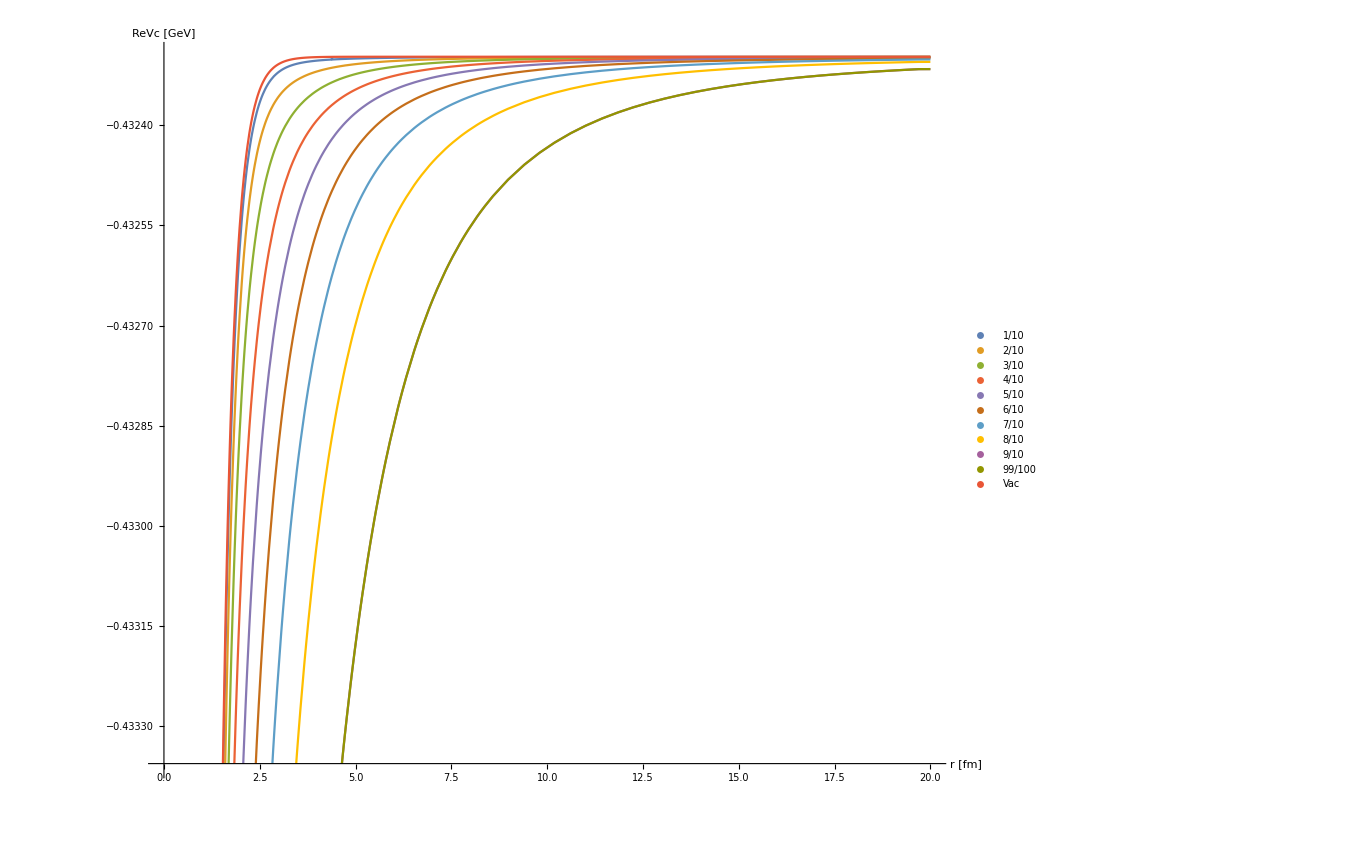

```mathematica
Plot[{ReVcu[1][r/0.197],ReVcu[2][r/0.197],ReVcu[3][r/0.197],ReVcu[4][r/0.197],ReVcu[5][r/0.197],ReVcu[6][r/0.197],ReVcu[7][r/0.197],ReVcu[8][r/0.197],ReVcu[9][r/0.197],ReVcu[9][r/0.197],ReV[r/0.197,mD1,αcont[[1]],0,ccont[[1]]]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.2}],BaseStyle->{FontSize->14}]
```

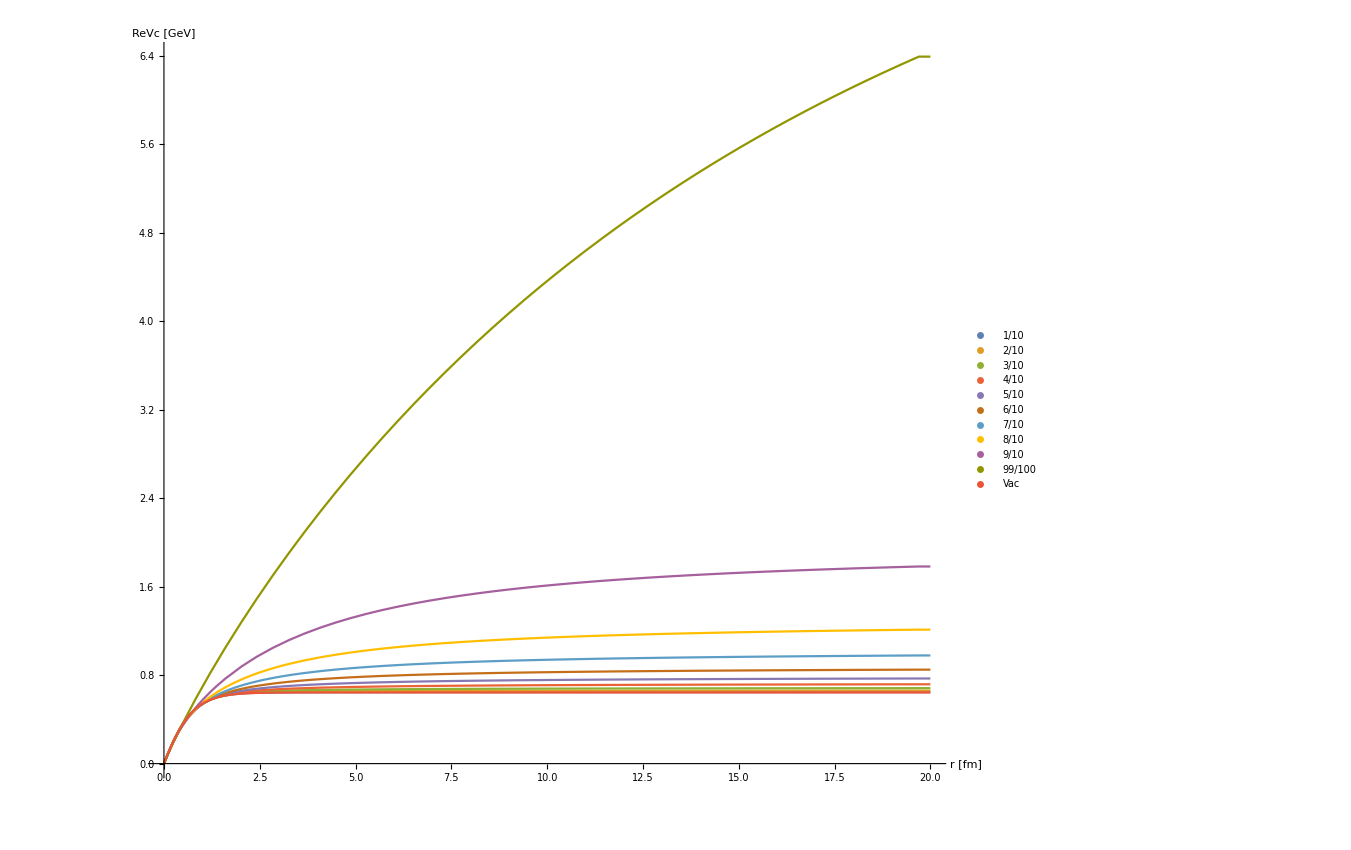

```mathematica
Plot[{ReVsu[1][r/0.197],ReVsu[2][r/0.197],ReVsu[3][r/0.197],ReVsu[4][r/0.197],ReVsu[5][r/0.197],ReVsu[6][r/0.197],ReVsu[7][r/0.197],ReVsu[8][r/0.197],ReVsu[9][r/0.197],ReVsu[10][r/0.197],ReV[r/0.197,mD1,0,σcont[[1]],0]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.2}],BaseStyle->{FontSize->14},PlotRange->All]
```

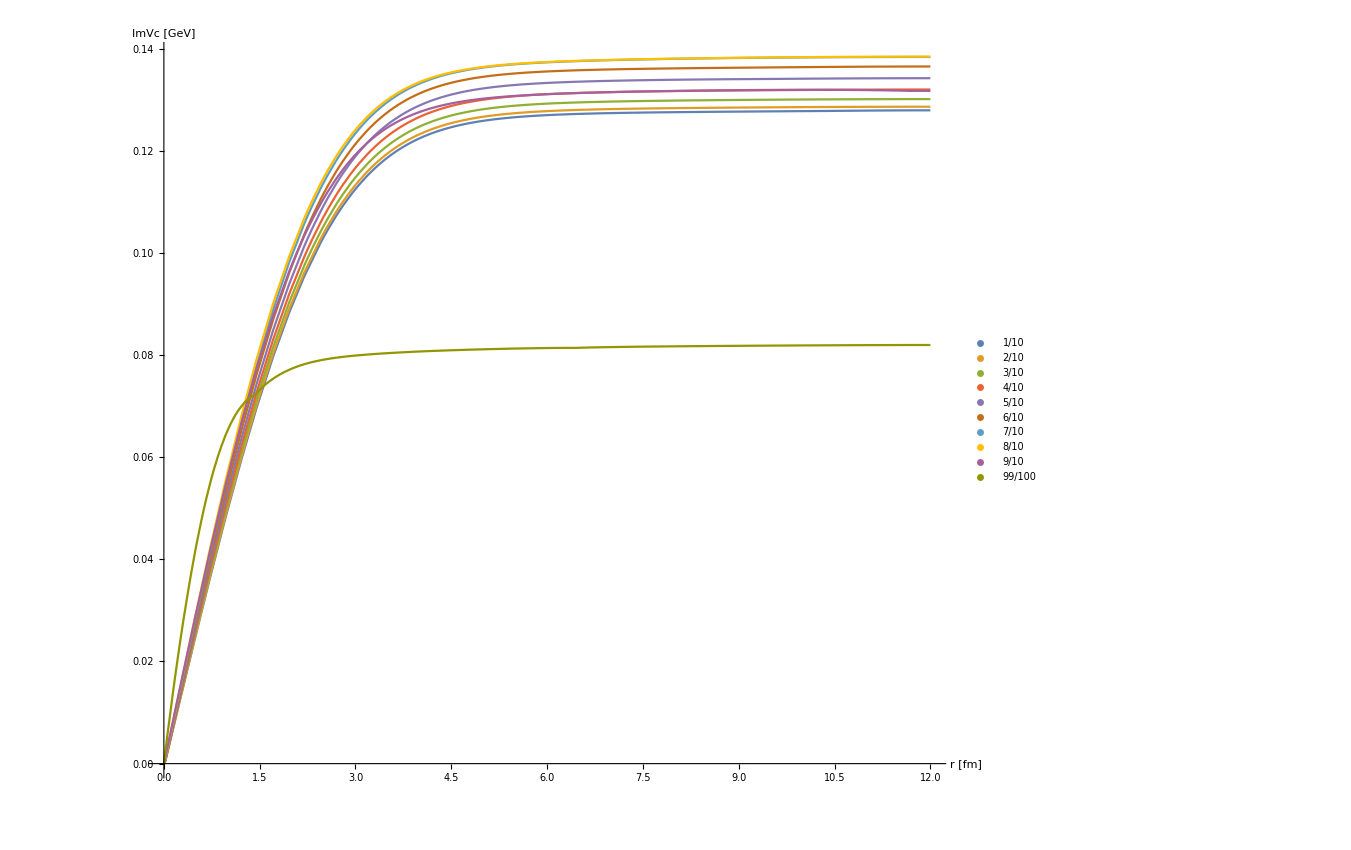

```mathematica
Plot[{Re[ImVcu[1][r/0.197]],Re[ImVcu[2][r/0.197]],Re[ImVcu[3][r/0.197]],Re[ImVcu[4][r/0.197]],Re[ImVcu[5][r/0.197]],Re[ImVcu[6][r/0.197]],Re[ImVcu[7][r/0.197]],Re[ImVcu[8][r/0.197]],Re[ImVcu[9][r/0.197]],Re[ImVcu[10][r/0.197]]},{r,1/1000,12},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14},PlotRange->All]
```

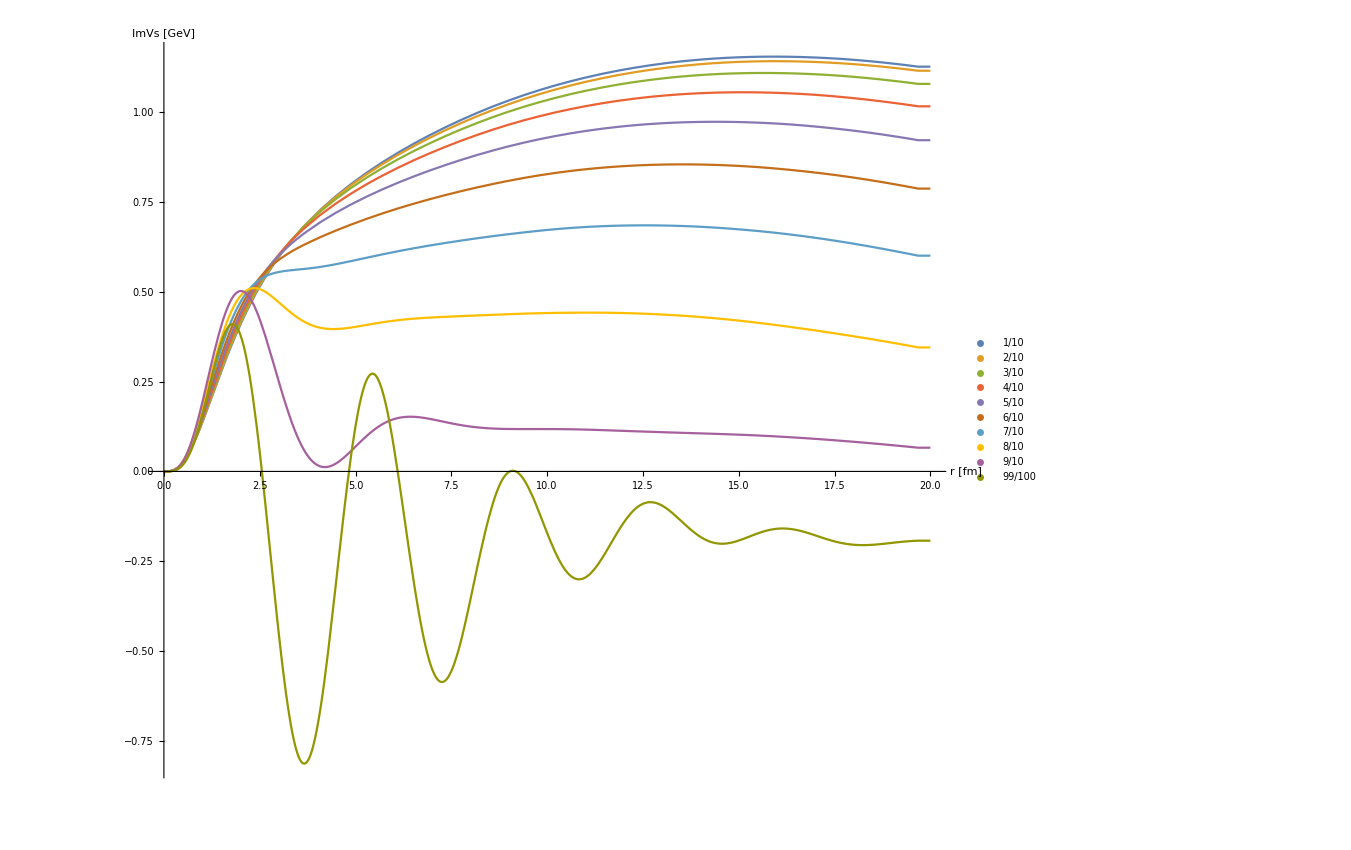

```mathematica
Plot[{Re[ImVsu[1][r/0.197]],Re[ImVsu[2][r/0.197]],Re[ImVsu[3][r/0.197]],Re[ImVsu[4][r/0.197]],Re[ImVsu[5][r/0.197]],Re[ImVsu[6][r/0.197]],Re[ImVsu[7][r/0.197]],Re[ImVsu[8][r/0.197]],Re[ImVsu[9][r/0.197]],Re[ImVsu[10][r/0.197]]},{r,1/1000,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

## Spectra

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s-wave

```mathematica
swaveccspectra[u_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc_perp/swccu"<>ToString[Round[10u]]<>"spectraT250.dat",Sort[ccss]];
];
```

```mathematica
swavebbspectra[u_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb_perp/swbbu"<>ToString[Round[10u]]<>"spectraT250.dat",Sort[ccss]];
];
```

```mathematica
swaveccspectra[10]
```

```mathematica
swavebbspectra[10]
```

```mathematica
Do[swaveccspectra[i],{i,1,9}]
```

```mathematica
Do[swavebbspectra[i],{i,1,9}]
```

## BW fit

### Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fit[input_,output_,Tscan_]:=Module[{temp=Range[1,Length[Tscan]],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];(*maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,0,1/2(maxx-minx),1/20}],First][[All,2]]]];*)
maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,Length[Tscan]}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])( const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];];
```

```mathematica
fitONE[input_]:=Module[{maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxis,mins,hwhmi,bad},
maxx=Max[input[[All,1]]];
minx=Min[input[[All,1]]];
maxy=Max[input[[All,2]]];
maxyx=input[[Position[input,Max[input[[All,2]]]][[1,1]],1]];
maxyi=Position[input[[All,1]],maxyx][[1,1]];
maxxy=input[[Position[input,Max[input[[All,1]]]][[1,1]],2]];
inter=Interpolation[input,InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}],maxxy/30],FindArgMax[{inter[x],minx+a≤x≤minx+2 a},{x,minx+a}][[1]]},{a,1,1/2(maxx-minx),1/20}],First][[All,2]]]];bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[[All,1]],Nearest[input[[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[[maxxis[[i]]-30,2]]>input[[maxxis[[i]],2]],input[[maxxis[[i]]+30,2]]>input[[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[[All,2]],Min[input[[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input]]];,
hwhmi=Position[input,Nearest[input[[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input],maxyi+3(maxyi-hwhmi),Length[input]]};];
If[mins[[1]]≤0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input,Nearest[input[[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];];
```

### Fitting

```mathematica
uscanI={1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1};
```

#### Charmonium Tc

```mathematica
Do[ccdata[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatau[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatal[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscan]}];
```

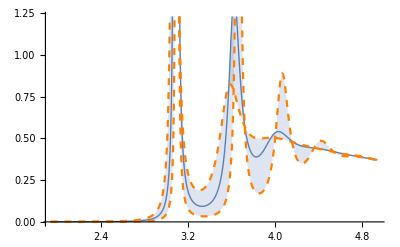

```mathematica
Block[{n=10},ListPlot[{ccdata[n],ccdatal[n],ccdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
Quiet[fit[ccdatal,ccmodell,uscanI]];
Quiet[fit[ccdatau,ccmodelu,uscanI]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

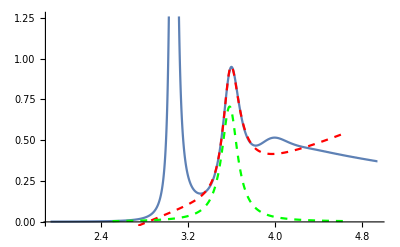

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

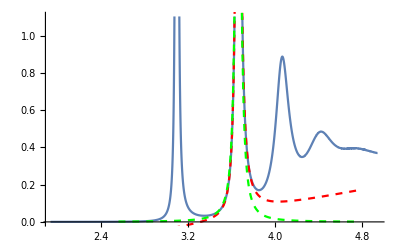

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

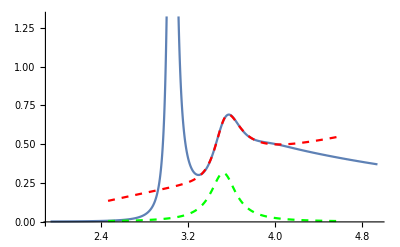

```mathematica
Block[{i=7,ii=2},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]],wrfitccu[[All,1]],wrfitccl[[All,1]]}]
```

{{1/10,3.06637,3.03909,3.08597},{1/5,3.06681,3.03972,3.08621},{3/10,3.06755,3.0408,3.08661},{2/5,3.06865,3.04238,3.0872},{1/2,3.07014,3.04457,3.088},{3/5,3.07212,3.04752,3.08903},{7/10,3.07472,3.05147,3.09037},{4/5,3.07816,3.05683,3.0921},{9/10,3.08284,3.06432,3.09436},{99/100,3.08789,3.07263,3.09665}}

```mathematica
wrfitcc1={{1/10,3.0663689453922336,3.0390934656531807,3.0859692271996244},{1/5,3.0668058473417936,3.0397189900325867,3.0862075210146163},{3/10,3.067553741431351,3.0407966528799637,3.0866133652423136},{2/5,3.0686467685604537,3.0423830812866726,3.08720153774853},{1/2,3.070138878635057,3.044574243254233,3.0879956588139197},{3/5,3.07211585767268,3.0475203363172256,3.089032572045881},{7/10,3.074715021207178,3.051466039196709,3.0903697028304995},{4/5,3.0781636158116403,3.0568255778981985,3.092099855706263},{9/10,3.0828419814504264,3.0643190101985134,3.094364697696784},{99/100,3.0878877753430474,3.0726269872021166,3.0966521743257807}};
```

```mathematica
Transpose[{uscan,wrfitcc[[All,2]],wrfitccu[[All,2]],wrfitccl[[All,2]]}]
```

{{1/10,3.58138,3.50479,3.64311},{1/5,3.58193,3.50523,3.64344},{3/10,3.58348,3.50659,3.64401},{2/5,3.58467,3.50861,3.64486},{1/2,3.58697,3.51158,3.64602},{3/5,3.59021,3.51607,3.64759},{7/10,3.59489,3.52306,3.64967},{4/5,3.60088,3.53321,3.65248},{9/10,3.60973,3.54906,3.65628},{99/100,3.61817,3.56043,3.65978}}

```mathematica
wrfitcc2={{1/10,3.5813775407158297,3.5047947648818103,3.6431094799172543},{1/5,3.5819343458071082,3.5052295758486096,3.643440357700103},{3/10,3.5834798258904614,3.5065897060179534,3.644013145006523},{2/5,3.584665296790009,3.5086139627615878,3.6448562527619366},{1/2,3.586967002758437,3.51157760358517,3.6460228958882888},{3/5,3.5902108415435894,3.5160670342632545,3.6475910324616403},{7/10,3.5948912045016255,3.5230573616818277,3.649673992214731},{4/5,3.6008818600571852,3.5332122262867602,3.65247795733201},{9/10,3.609731951966939,3.549055257458368,3.656281199189587},{99/100,3.618172131285003,3.5604329339917355,3.659776357492796}};
```

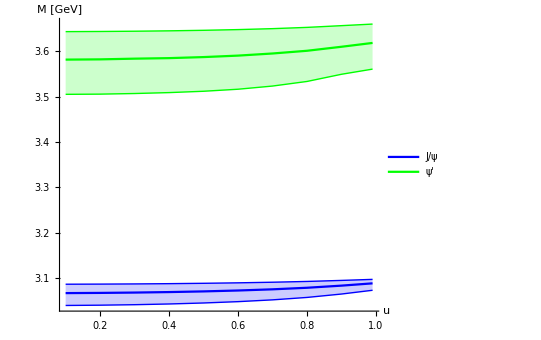

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfitcc1[[;;,2]]}],Transpose[{uscan[[;;]],wrfitcc1[[;;,3]]}],Transpose[{uscan[[;;]],wrfitcc1[[;;,4]]}],Transpose[{uscan[[;;]],wrfitcc2[[;;,2]]}],Transpose[{uscan[[;;]],wrfitcc2[[;;,3]]}],Transpose[{uscan[[;;]],wrfitcc2[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Transpose[{uscan,gfitcc[[All,1]],gfitccu[[All,1]],gfitccl[[All,1]]}]
```

{{1/10,0.0350962,0.0574362,0.0156346},{1/5,0.0351578,0.0576631,0.0156238},{3/10,0.0352459,0.058021,0.0155985},{2/5,0.0353337,0.0584792,0.015544},{1/2,0.0353729,0.0589657,0.015437},{3/5,0.0352718,0.0593501,0.0152328},{7/10,0.0348486,0.059353,0.0148476},{4/5,0.0336791,0.0582929,0.0140898},{9/10,0.0304404,0.053974,0.012385},{99/100,0.0169017,0.0319523,0.0063985}}

```mathematica
gfitcc1={{1/10,0.03509623614433616,0.05743619681659198,0.015634603134638082},{1/5,0.03515775412941795,0.057663126758552674,0.015623773826675964},{3/10,0.03524592325311088,0.05802096543426276,0.015598487673072769},{2/5,0.03533374179543238,0.05847919069792092,0.015544007120240158},{1/2,0.03537285730864292,0.058965720435645734,0.015437037413929038},{3/5,0.03527177743217072,0.0593500963489929,0.015232824038684643},{7/10,0.03484858267752482,0.05935303798752198,0.014847644044053806},{4/5,0.03367905357788095,0.05829293395886445,0.014089849157962955},{9/10,0.030440403835104164,0.0539740069035063,0.012385039037227874},{99/100,0.01690172487365056,0.03195231759866381,0.006398496551710401}};
```

```mathematica
Transpose[{uscan,gfitcc[[All,2]],gfitccu[[All,2]],gfitccl[[All,2]]}]
```

{{1/10,0.176253,0.248834,0.0934501},{1/5,0.177102,0.250883,0.0936502},{3/10,0.178397,0.254801,0.0939326},{2/5,0.180679,0.259861,0.0942564},{1/2,0.182799,0.265861,0.0944707},{3/5,0.185277,0.273122,0.0943689},{7/10,0.187057,0.27982,0.0935104},{4/5,0.186475,0.285328,0.0907741},{9/10,0.178167,0.280874,0.0827284},{99/100,0.120935,0.205619,0.0469587}}

```mathematica
gfitcc2={{1/10,0.17625321159126014,0.24883366467103013,0.09345008068864988},{1/5,0.17710245174984104,0.25088338350745293,0.09365015485532839},{3/10,0.1783970370174799,0.2548014129315289,0.09393257959213677},{2/5,0.1806791359674714,0.25986100158180736,0.09425635323046107},{1/2,0.1827994237453654,0.2658606600650281,0.09447073853344325},{3/5,0.1852766065287437,0.2731221067163092,0.09436891611205724},{7/10,0.18705652960803082,0.27982048781387053,0.09351042268216267},{4/5,0.18647466551533431,0.2853277181357263,0.09077407251580498},{9/10,0.17816665360374812,0.2808738740156078,0.08272837597957543},{99/100,0.1209353789598855,0.20561862850401713,0.046958743492029734}};
```

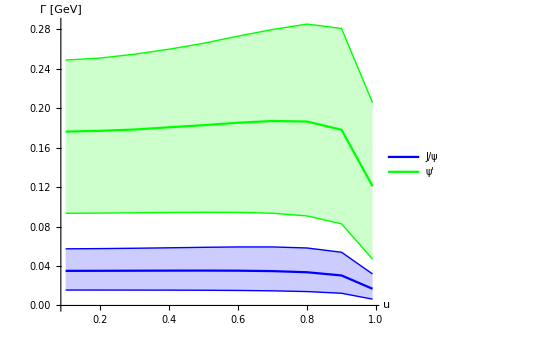

```mathematica
ListPlot[{Transpose[{uscan[[;;]],gfitcc1[[;;,2]]}],Transpose[{uscan[[;;]],gfitcc1[[;;,3]]}],Transpose[{uscan[[;;]],gfitcc1[[;;,4]]}],Transpose[{uscan[[;;]],gfitcc2[[;;,2]]}],Transpose[{uscan[[;;]],gfitcc2[[;;,3]]}],Transpose[{uscan[[;;]],gfitcc2[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

#### Bottomonium Tc

```mathematica
Do[bbdata[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectra.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatau[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectrau.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatal[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectral.dat"];,{n,Length[uscan]}];
```

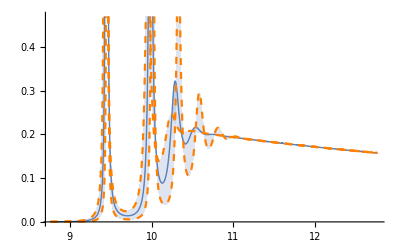

```mathematica
Block[{n=1},ListPlot[{bbdata[n],bbdatal[n],bbdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,uscanI]];
Quiet[fit[bbdatal,bbmodell,uscanI]];
Quiet[fit[bbdatau,bbmodelu,uscanI]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

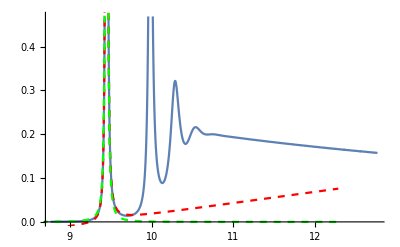

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

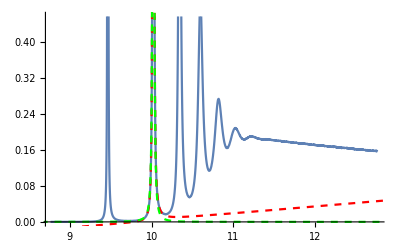

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

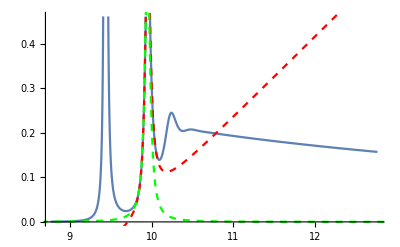

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitbb[[All,1]],wrfitbbu[[All,1]],wrfitbbl[[All,1]]}]
```

{{1/10,9.4485,9.43744,9.45602},{1/5,9.44889,9.43801,9.45623},{3/10,9.44954,9.43898,9.45659},{2/5,9.45048,9.44037,9.4571},{1/2,9.45175,9.44226,9.45779},{3/5,9.45338,9.44471,9.45867},{7/10,9.45547,9.44786,9.45978},{4/5,9.45813,9.45192,9.46118},{9/10,9.46152,9.4572,9.46293},{99/100,9.46473,9.46248,9.46447}}

```mathematica
wrfitbb1={{1/10,9.44850057715624,9.437442205342954,9.456021104328052},{1/5,9.448885372754175,9.438009463361553,9.4562320298245},{3/10,9.449539216294518,9.438975102410682,9.456590008747193},{2/5,9.450482728817343,9.440372355044065,9.457103045662612},{1/2,9.451747836976256,9.442255098080404,9.457788951714488},{3/5,9.453384979917223,9.444706476471465,9.458670802355794},{7/10,9.45547154065031,9.447857620450897,9.459783729359778},{4/5,9.458127110183097,9.451916273261297,9.461181896302797},{9/10,9.461519428047483,9.457199599937889,9.462929535512176},{99/100,9.464727582919405,9.462476117840772,9.464469772234226}};
```

```mathematica
Transpose[{uscan,wrfitbb[[All,2]],wrfitbbu[[All,2]],wrfitbbl[[All,2]]}]
```

{{1/10,9.98422,9.95023,10.009},{1/5,9.98468,9.95085,10.0093},{3/10,9.98546,9.952,10.0097},{2/5,9.98661,9.95362,10.0103},{1/2,9.98819,9.95594,10.0112},{3/5,9.99031,9.95906,10.0123},{7/10,9.99311,9.96329,10.0137},{4/5,9.99689,9.96914,10.0156},{9/10,10.0021,9.9775,10.0181},{99/100,10.008,9.98705,10.0207}}

```mathematica
wrfitbb2={{1/10,9.98422111782614,9.950227436568388,10.009047482441527},{1/5,9.984676157667005,9.9508546053834,10.00929741279056},{3/10,9.985460442136203,9.951998895751876,10.0097235860625},{2/5,9.986611212664238,9.95361639823814,10.010343111268174},{1/2,9.988193366691299,9.955940530194441,10.011183432732665},{3/5,9.990305616852085,9.959057777875975,10.012286559591614},{7/10,9.993114540620038,9.963287426535535,10.013720741094188},{4/5,9.996892155218609,9.969135781889975,10.015594462656255},{9/10,10.002118270727061,9.977497647747285,10.018086648003711},{99/100,10.007996402701894,9.987050475979226,10.020710641277715}};
```

```mathematica
Transpose[{uscan,wrfitbb[[All,3]],wrfitbbu[[All,3]],wrfitbbl[[All,3]]}]
```

{{1/10,10.2813,10.2155,10.327},{1/5,10.2781,10.2165,10.3273},{3/10,10.2789,10.2173,10.3278},{2/5,10.284,10.2196,10.3285},{1/2,10.2823,10.2233,10.3296},{3/5,10.285,10.2264,10.3309},{7/10,10.2885,10.2333,10.3328},{4/5,10.294,10.2414,10.3352},{9/10,10.3013,10.2529,10.3386},{99/100,10.3108,10.2652,10.3422}}

```mathematica
wrfitbb3={{1/10,10.281308712216072,10.215453229283725,10.326960165478548},{1/5,10.278062123229603,10.216453190925153,10.327250282007036},{3/10,10.278922996286353,10.217268568754656,10.327775430304236},{2/5,10.283957337909403,10.219627191997617,10.32853294800252},{1/2,10.282258692698935,10.223285404692962,10.329564411519678},{3/5,10.285027382731291,10.226378222130657,10.330924569884452},{7/10,10.288500098007505,10.233337182116937,10.332763570422726},{4/5,10.293980037155187,10.241406531758209,10.335235151811645},{9/10,10.301321635854501,10.252877614565126,10.338606045758276},{99/100,10.310802456731462,10.265221132714483,10.342228023605566}};
```

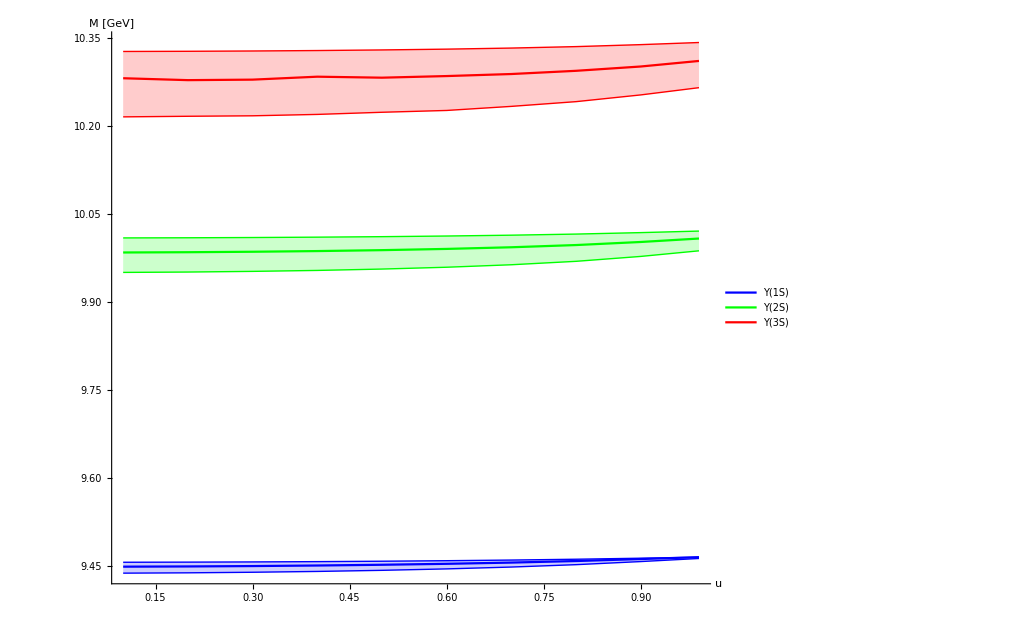

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfitbb1[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb1[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb1[[;;,4]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb2[[;;,4]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,3]]}],Transpose[{uscan[[;;]],wrfitbb3[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None,Style["Υ(3S)",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Transpose[{uscan,gfitbb[[All,1]],gfitbbu[[All,1]],gfitbbl[[All,1]]}]
```

{{1/10,0.00738667,0.0126786,0.00307764},{1/5,0.00737527,0.0126736,0.00306854},{3/10,0.00735164,0.012659,0.00305036},{2/5,0.00730928,0.0126239,0.00302305},{1/2,0.00723688,0.0125489,0.00297937},{3/5,0.00711366,0.0123987,0.00291069},{7/10,0.00689785,0.0121046,0.00279992},{4/5,0.00650054,0.0115117,0.00261017},{9/10,0.00565336,0.0101518,0.00223109},{99/100,0.0028416,0.00528984,0.00107254}}

```mathematica
gfitbb1={{1/10,0.00738667140489188,0.012678580135118784,0.0030776439465828504},{1/5,0.007375271851376379,0.012673564304510951,0.0030685427032178525},{3/10,0.007351637130377281,0.012658958526613466,0.003050361568656736},{2/5,0.007309279747997597,0.012623918574300627,0.0030230469689283305},{1/2,0.0072368805496368675,0.012548890123624193,0.0029793690338808486},{3/5,0.007113662758503195,0.012398683530073892,0.0029106851751723698},{7/10,0.006897852716221106,0.012104624337847272,0.0027999206510812454},{4/5,0.006500544778925407,0.011511705562737307,0.002610167540653337},{9/10,0.005653364362888479,0.010151779069869055,0.0022310889082230168},{99/100,0.0028415967857800865,0.005289842045874265,0.001072544839667232}};
```

```mathematica
Transpose[{uscan,gfitbb[[All,2]],gfitbbu[[All,2]],gfitbbl[[All,2]]}]
```

{{1/10,0.0476739,0.0765324,0.0213499},{1/5,0.0477663,0.0768592,0.0213365},{3/10,0.0478998,0.0772747,0.021304},{2/5,0.0480391,0.0780277,0.0212334},{1/2,0.0481172,0.078649,0.021092},{3/5,0.0480121,0.0792582,0.0208189},{7/10,0.0474745,0.0793946,0.020298},{4/5,0.0459332,0.0782502,0.0192694},{9/10,0.0415782,0.0728634,0.0169452},{99/100,0.0231272,0.0436857,0.00875864}}

```mathematica
gfitbb2={{1/10,0.047673949000464025,0.07653239332699067,0.02134986945608235},{1/5,0.04776628697789676,0.07685920634000984,0.021336500348199703},{3/10,0.04789979277547312,0.07727466909105475,0.02130403556717},{2/5,0.04803912612471308,0.07802766552317551,0.021233402349420675},{1/2,0.0481172251269611,0.07864899156451685,0.02109195343647033},{3/5,0.04801212227028091,0.07925817285983457,0.020818859759866033},{7/10,0.04747449361865648,0.07939457421838048,0.02029800831328093},{4/5,0.045933221418702194,0.07825021997809167,0.01926936317293007},{9/10,0.04157822515135499,0.07286341592538396,0.016945174773009494},{99/100,0.023127229354214875,0.043685741898337814,0.008758639548419496}};
```

```mathematica
Transpose[{uscan,gfitbb[[All,3]],gfitbbu[[All,3]],gfitbbl[[All,3]]}]
```

{{1/10,0.110706,0.15777,0.0611815},{1/5,0.116872,0.157878,0.0612599},{3/10,0.117735,0.160153,0.0612993},{2/5,0.113138,0.161887,0.0613717},{1/2,0.119625,0.16483,0.0613303},{3/5,0.120641,0.167713,0.061088},{7/10,0.121259,0.17077,0.0601987},{4/5,0.119899,0.172407,0.0580282},{9/10,0.113658,0.169739,0.0523242},{99/100,0.0738625,0.122721,0.0287306}}

```mathematica
gfitbb3={{1/10,0.11070585204584911,0.15776976844952623,0.061181452108719024},{1/5,0.1168717447870786,0.1578781324702774,0.06125985494307562},{3/10,0.11773501277968197,0.1601532233439504,0.061299295806732185},{2/5,0.11313823000397731,0.1618869970396518,0.06137173170794632},{1/2,0.11962455894279599,0.16482962967263817,0.06133025456088586},{3/5,0.12064052980055034,0.16771306878697348,0.06108803137590968},{7/10,0.12125878183306399,0.17076992243950473,0.060198715125607656},{4/5,0.11989921142504663,0.17240705999446687,0.058028176290812465},{9/10,0.11365804754149299,0.16973902547909717,0.052324223424020495},{99/100,0.07386252392637095,0.12272086945829737,0.02873058618103025}};
```

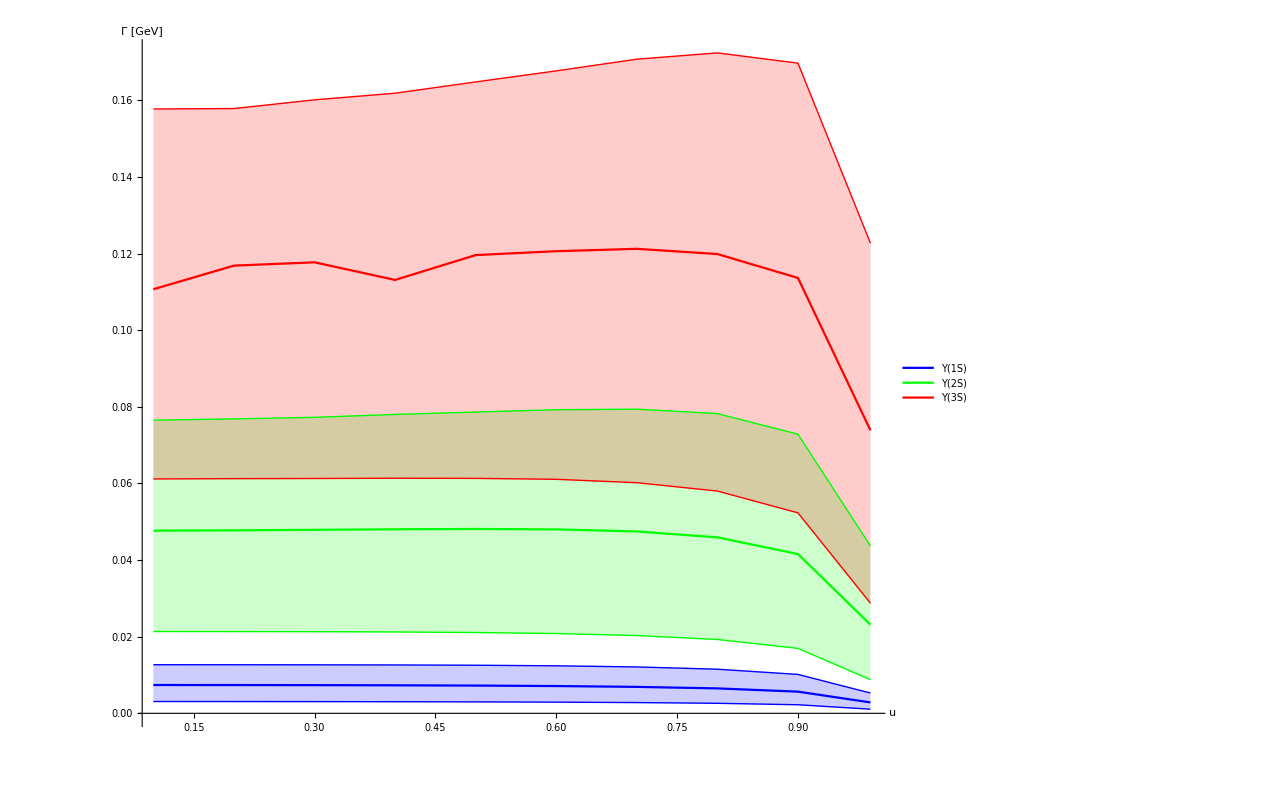

```mathematica
ListPlot[{Transpose[{uscan[[;;]],gfitbb1[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb1[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb1[[;;,4]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb2[[;;,4]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,2]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,3]]}],Transpose[{uscan[[;;]],gfitbb3[[;;,4]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"],None,None,Style["Υ(3S)",25,"Helvetica"]}],{0.8,0.4}]]
```

#### Charmonium 250 MeV

```mathematica
Do[ccdata[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatau[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250u.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[ccdatal[n]=Import["cc/swccu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250l.dat"];,{n,Length[uscan]}];
```

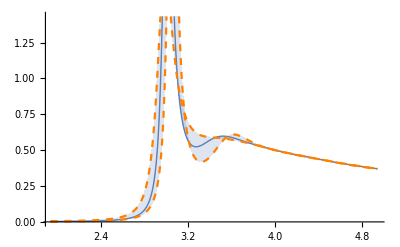

```mathematica
Block[{n=10},ListPlot[{ccdata[n],ccdatal[n],ccdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[ccmodelu,ccmodell,ccmodel]
Quiet[fit[ccdata,ccmodel,uscanI]];
Quiet[fit[ccdatal,ccmodell,uscanI]];
Quiet[fit[ccdatau,ccmodelu,uscanI]];
```

```mathematica
Clear[wrfitcc,wrfitccl,wrfitccu,gfitcc,gfitccl,gfitccu,areafitcc,areafitccu,areafitccl,cfitcc,cfitccl,cfitccu,dfitcc,dfitccl,dfitccu,sfitcc,sfitccl,sfitccu,s2fitcc,s2fitccl,s2fitccu];
store[wr,wrfitcc,ccmodel];
store[wr,wrfitccl,ccmodell];
store[wr,wrfitccu,ccmodelu];
store[Γ,gfitcc,ccmodel];
store[Γ,gfitccl,ccmodell];
store[Γ,gfitccu,ccmodelu];
store[const,cfitcc,ccmodel];
store[const,cfitccl,ccmodell];
store[const,cfitccu,ccmodelu];
store[δbg,dfitcc,ccmodel];
store[δbg,dfitccl,ccmodell];
store[δbg,dfitccu,ccmodelu];
store[shift,sfitcc,ccmodel];
store[shift,sfitccl,ccmodell];
store[shift,sfitccu,ccmodelu];
store[shift2,s2fitcc,ccmodel];
store[shift2,s2fitccl,ccmodell];
store[shift2,s2fitccu,ccmodelu];
storearea[areafitcc,ccmodel];
storearea[areafitccl,ccmodell];
storearea[areafitccu,ccmodelu];
```

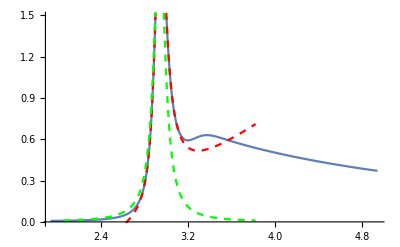

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdata[i],Joined->True],Plot[BW[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],dfitcc[[i,ii]],cfitcc[[i,ii]],sfitcc[[i,ii]],s2fitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitcc[[i,ii]],gfitcc[[i,ii]],cfitcc[[i,ii]]],{x,0.7wrfitcc[[i,ii]],1.3wrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

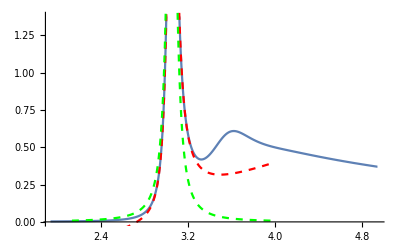

```mathematica
Block[{i=10,ii=1},Show[{ListPlot[ccdatal[i],Joined->True],Plot[BW[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],dfitccl[[i,ii]],cfitccl[[i,ii]],sfitccl[[i,ii]],s2fitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccl[[i,ii]],gfitccl[[i,ii]],cfitccl[[i,ii]]],{x,0.7wrfitccl[[i,ii]],1.3wrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

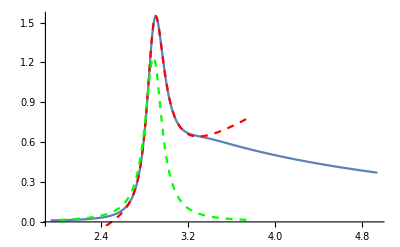

```mathematica
Block[{i=1,ii=1},Show[{ListPlot[ccdatau[i],Joined->True],Plot[BW[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],dfitccu[[i,ii]],cfitccu[[i,ii]],sfitccu[[i,ii]],s2fitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitccu[[i,ii]],gfitccu[[i,ii]],cfitccu[[i,ii]]],{x,0.7wrfitccu[[i,ii]],1.3wrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitcc[[All,1]],wrfitccu[[All,1]],wrfitccl[[All,1]]}]
```

{{1/10,2.93849,2.88256,3.00182},{1/5,2.93946,2.88378,3.00276},{3/10,2.94114,2.88594,3.00437},{2/5,2.94369,2.88923,3.00675},{1/2,2.94737,2.89413,3.01006},{3/5,2.95256,2.90113,3.01454},{7/10,2.95999,2.91136,3.02057},{4/5,2.97084,2.92642,3.02877},{9/10,2.98724,2.94901,3.04003},{99/100,3.00542,2.97063,3.04957}}

```mathematica
Transpose[{uscan,gfitcc[[All,1]],gfitccu[[All,1]],gfitccl[[All,1]]}]
```

{{1/10,0.121779,0.190864,0.135141},{1/5,0.122927,0.19307,0.135871},{3/10,0.12484,0.196813,0.137077},{2/5,0.127624,0.202139,0.138683},{1/2,0.131087,0.209035,0.140598},{3/5,0.135274,0.217263,0.14254},{7/10,0.139633,0.226165,0.14393},{4/5,0.142868,0.23352,0.143362},{9/10,0.140075,0.232118,0.136105},{99/100,0.0977839,0.175447,0.0886082}}

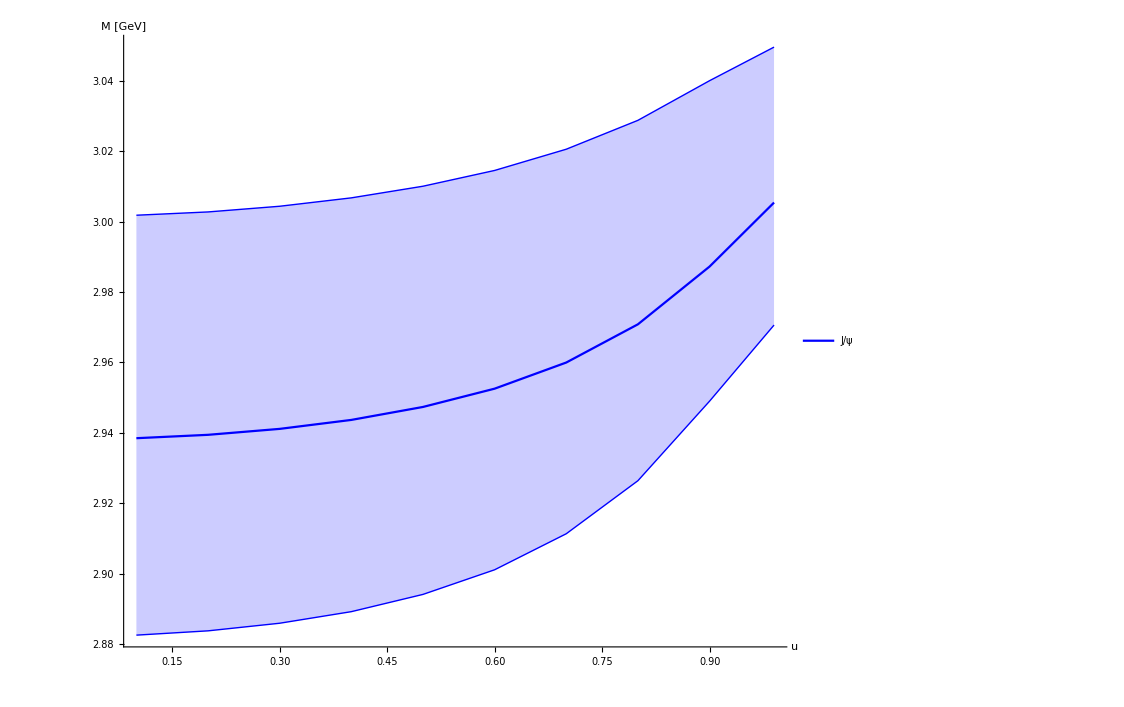

```mathematica
ListPlot[{Transpose[{uscan,wrfitcc[[;;,1]]}],Transpose[{uscan,wrfitccl[[;;,1]]}],Transpose[{uscan,wrfitccu[[;;,1]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

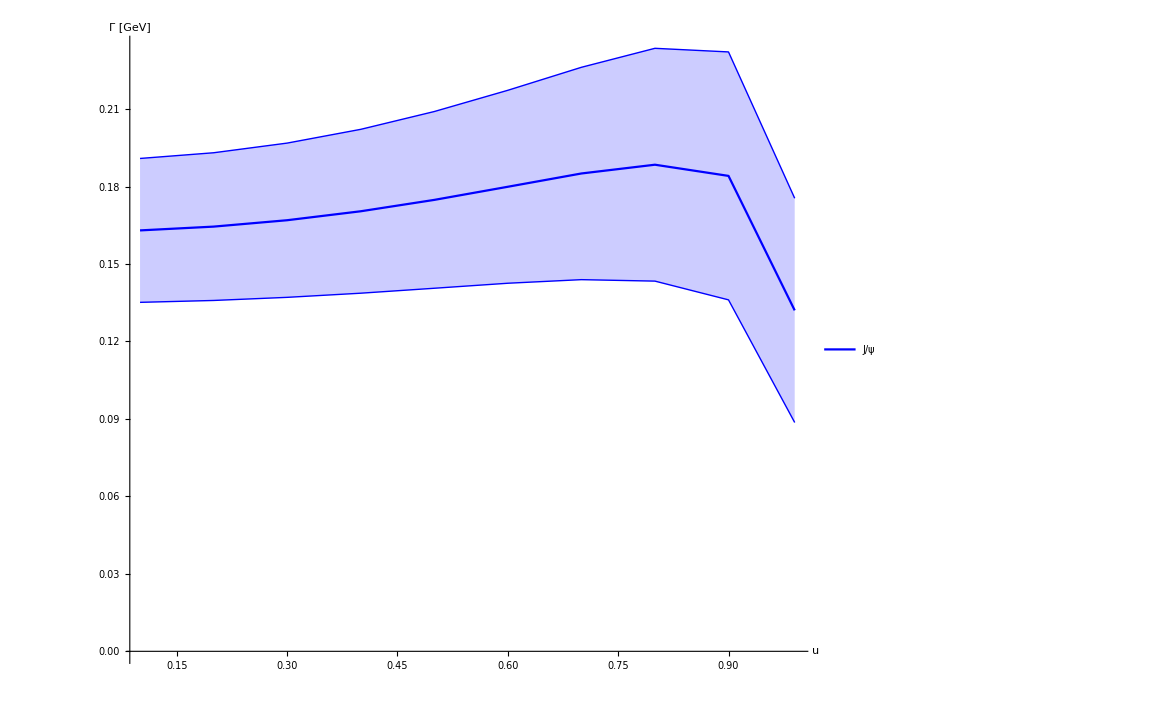

```mathematica
ListPlot[{Transpose[{uscan,1/2(gfitccu[[;;,1]]+gfitccl[[;;,1]])}],Transpose[{uscan,gfitccl[[;;,1]]}],Transpose[{uscan,gfitccu[[;;,1]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6}},PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Darker[Green],{Darker[Green],Thin},{Darker[Green],Thin},Gray,{Gray,Thin},{Gray,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["J/ψ",25,"Helvetica"],None,None,Style["ψ'",25,"Helvetica"]}],{0.8,0.2}]]
```

#### Bottomonium 250 MeV

```mathematica
Do[bbdata[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatau[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250u.dat"];,{n,Length[uscan]}];
```

```mathematica
Do[bbdatal[n]=Import["bb/swbbu"<>ToString[Round[100uscanI[[n]]]]<>"spectraT250l.dat"];,{n,Length[uscan]}];
```

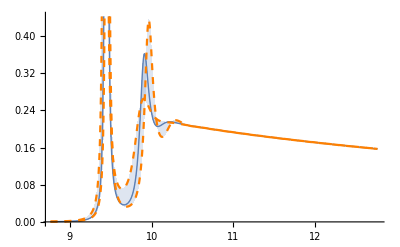

```mathematica
Block[{n=10},ListPlot[{bbdata[n],bbdatal[n],bbdatau[n]},Joined->True,Filling->{1->{2},1->{3}},PlotStyle->{Thick,{Dashed,Orange},{Dashed,Orange}}]]
```

```mathematica
Clear[bbmodelu,bbmodell,bbmodel]
Quiet[fit[bbdata,bbmodel,uscanI]];
Quiet[fit[bbdatal,bbmodell,uscanI]];
Quiet[fit[bbdatau,bbmodelu,uscanI]];
```

```mathematica
Clear[wrfitbb,wrfitbbl,wrfitbbu,gfitbb,gfitbbl,gfitbbu,areafitbb,areafitbbu,areafitbbl,cfitbb,cfitbbl,cfitbbu,dfitbb,dfitbbl,dfitbbu,sfitbb,sfitbbl,sfitbbu,s2fitbb,s2fitbbl,s2fitbbu];
store[wr,wrfitbb,bbmodel];
store[wr,wrfitbbl,bbmodell];
store[wr,wrfitbbu,bbmodelu];
store[Γ,gfitbb,bbmodel];
store[Γ,gfitbbl,bbmodell];
store[Γ,gfitbbu,bbmodelu];
store[const,cfitbb,bbmodel];
store[const,cfitbbl,bbmodell];
store[const,cfitbbu,bbmodelu];
store[δbg,dfitbb,bbmodel];
store[δbg,dfitbbl,bbmodell];
store[δbg,dfitbbu,bbmodelu];
store[shift,sfitbb,bbmodel];
store[shift,sfitbbl,bbmodell];
store[shift,sfitbbu,bbmodelu];
store[shift2,s2fitbb,bbmodel];
store[shift2,s2fitbbl,bbmodell];
store[shift2,s2fitbbu,bbmodelu];
storearea[areafitbb,bbmodel];
storearea[areafitbbl,bbmodell];
storearea[areafitbbu,bbmodelu];
```

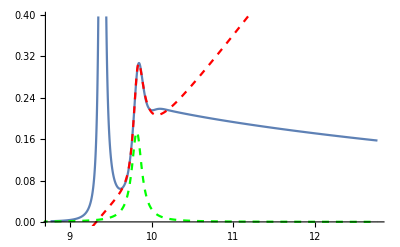

```mathematica
Block[{i=1,ii=2},Show[{ListPlot[bbdata[i],Joined->True],Plot[BW[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],dfitbb[[i,ii]],cfitbb[[i,ii]],sfitbb[[i,ii]],s2fitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbb[[i,ii]],gfitbb[[i,ii]],cfitbb[[i,ii]]],{x,0.7wrfitbb[[i,ii]],1.3wrfitbb[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

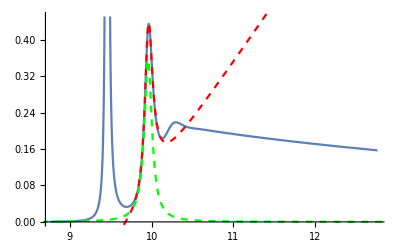

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[bbdatal[i],Joined->True],Plot[BW[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],dfitbbl[[i,ii]],cfitbbl[[i,ii]],sfitbbl[[i,ii]],s2fitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbl[[i,ii]],gfitbbl[[i,ii]],cfitbbl[[i,ii]]],{x,0.7wrfitbbl[[i,ii]],1.3wrfitbbl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

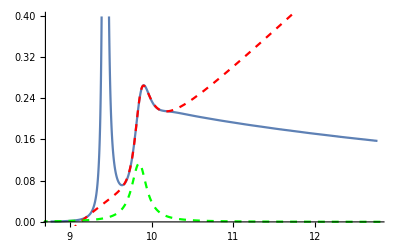

```mathematica
Block[{i=10,ii=2},Show[{ListPlot[bbdatau[i],Joined->True],Plot[BW[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],dfitbbu[[i,ii]],cfitbbu[[i,ii]],sfitbbu[[i,ii]],s2fitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,wrfitbbu[[i,ii]],gfitbbu[[i,ii]],cfitbbu[[i,ii]]],{x,0.7wrfitbbu[[i,ii]],1.3wrfitbbu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}]]
```

```mathematica
Transpose[{uscan,wrfitbb[[All,1]],wrfitbbu[[All,1]],wrfitbbl[[All,1]]}]
```

{{1/10,9.3931,9.36255,9.41924},{1/5,9.39416,9.36384,9.42004},{3/10,9.39595,9.36606,9.42141},{2/5,9.39858,9.36932,9.4234},{1/2,9.40215,9.37378,9.4261},{3/5,9.40688,9.37972,9.42963},{7/10,9.41309,9.3876,9.43421},{4/5,9.42132,9.39818,9.44018},{9/10,9.43252,9.41285,9.44809},{99/100,9.44495,9.42954,9.4563}}

```mathematica
Transpose[{uscan,wrfitbb[[All,2]],wrfitbbu[[All,2]],wrfitbbl[[All,2]]}]
```

{{1/10,9.81888,9.74796,9.89749},{1/5,9.81978,9.74907,9.89852},{3/10,9.82118,9.75073,9.90005},{2/5,9.82372,9.7537,9.90255},{1/2,9.82719,9.75789,9.90595},{3/5,9.8323,9.76505,9.91068},{7/10,9.84059,9.77559,9.91731},{4/5,9.85252,9.79201,9.92631},{9/10,9.87081,9.8187,9.93985},{99/100,9.89787,9.84675,9.95711}}

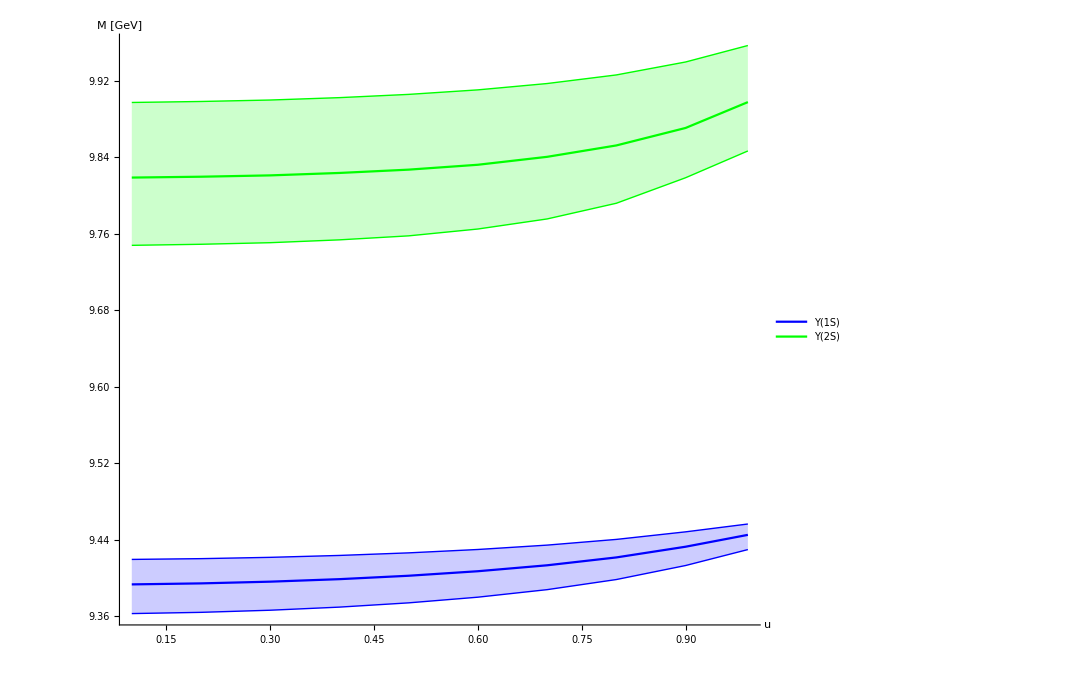

```mathematica
ListPlot[{Transpose[{uscan[[;;]],wrfitbb[[;;,1]]}],Transpose[{uscan[[;;]],wrfitbbl[[;;,1]]}],Transpose[{uscan[[;;]],wrfitbbu[[;;,1]]}],Transpose[{uscan[[;;]],wrfitbb[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbbl[[;;,2]]}],Transpose[{uscan[[;;]],wrfitbbu[[;;,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["M [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"]}],{0.8,0.4}]]
```

```mathematica
Transpose[{uscan,gfitbb[[All,1]],gfitbbu[[All,1]],gfitbbl[[All,1]]}]
```

{{1/10,0.02975,0.045509,0.032729},{1/5,0.0298233,0.0457028,0.03276},{3/10,0.0299341,0.0460166,0.0327974},{2/5,0.0300613,0.04642,0.0328151},{1/2,0.0301665,0.0468608,0.0327659},{3/5,0.0301742,0.047245,0.0325625},{7/10,0.029931,0.0473437,0.0320314},{4/5,0.029074,0.0466062,0.0307749},{9/10,0.0264545,0.0432445,0.0275664},{99/100,0.0148966,0.0256015,0.0149585}}

```mathematica
Transpose[{uscan,gfitbb[[All,2]],gfitbbu[[All,2]],gfitbbl[[All,2]]}]
```

{{1/10,0.147425,0.228761,0.165399},{1/5,0.148597,0.231698,0.16596},{3/10,0.151076,0.236281,0.167669},{2/5,0.154112,0.242879,0.169424},{1/2,0.158645,0.250892,0.172144},{3/5,0.164134,0.260935,0.174619},{7/10,0.169172,0.271395,0.176762},{4/5,0.174026,0.280722,0.176976},{9/10,0.172674,0.282501,0.169775},{99/100,0.12218,0.221617,0.113998}}

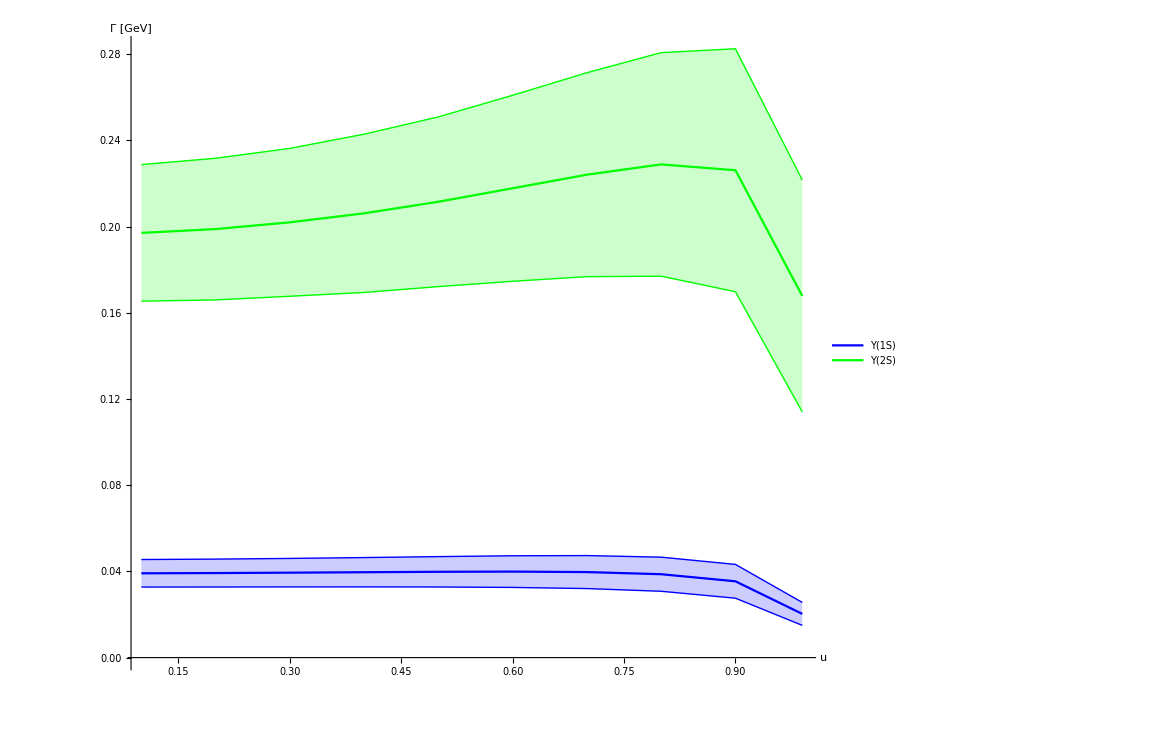

```mathematica
ListPlot[{Transpose[{uscan[[;;]],1/2(gfitbbu[[;;,1]]+gfitbbl[[;;,1]])}],Transpose[{uscan[[;;]],gfitbbl[[;;,1]]}],Transpose[{uscan[[;;]],gfitbbu[[;;,1]]}],Transpose[{uscan[[;;]],1/2(gfitbbu[[;;,2]]+gfitbbl[[;;,2]])}],Transpose[{uscan[[;;]],gfitbbl[[;;,2]]}],Transpose[{uscan[[;;]],gfitbbu[[;;,2]]}]},PlotRange->All,Filling->{1->{2},1->{3},4->{5},4->{6},7->{8},7->{9}},FillingStyle->Opacity[0.2],PlotStyle->{Blue,{Blue,Thin},{Blue,Thin},Green,{Green,Thin},{Green,Thin},Red,{Red,Thin},{Red,Thin}},Joined->True,AxesLabel->{Style["u",25,Black],Style["Γ [GeV]",25,Black]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,PlotLegends->Placed[LineLegend[{Style["Υ(1S)",25,"Helvetica"],None,None,Style["Υ(2S)",25,"Helvetica"]}],{0.8,0.4}]]
```